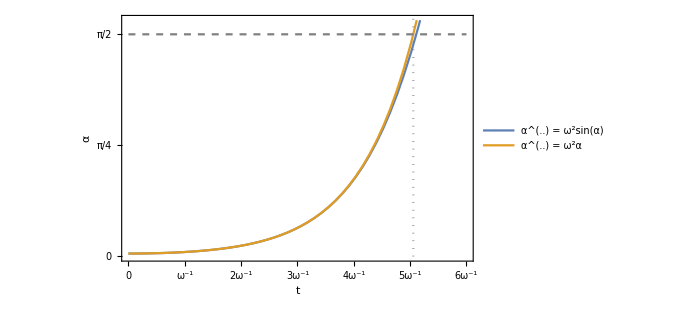

```mathematica
Clear["Global`*"];
a0=0.02;
tmax=6;
s1=NDSolve[{a''[t]==Sin[a[t]],a[0]==a0,a'[0]==0},a,{t,0,tmax}];
s2=NDSolve[{a''[t]==a[t],a[0]==a0,a'[0]==0},a,{t,0,tmax}];
l1="α^(..) = ω^2sin(α)";
l2="α^(..) = ω^2α";
range={{0,tmax},{0,Pi/2+0.1}};
Show[
Plot[{
Evaluate[a[t]/.s1],
Evaluate[a[t]/.s2]
},{t,0,tmax},
PlotRange->range,
ImageSize->500,
Frame->True,
Axes->False,
FrameTicks->{{{0,π/4,π/2},None},{{{0,0},{1,"ω^-1"},{2,"2ω^-1"},{3,"3ω^-1"},{4,"4ω^-1"},{5,"5ω^-1"},{6,"6ω^-1"}},None}},
PlotLegends->Placed[LineLegend[{l1,l2}],{Top,Right}],
FrameLabel->{"t","α"},
LabelStyle->{FontSize->16,FontFamily->"Georgia"}],
Plot[π/2,{t,0,tmax},
PlotRange->range,
PlotStyle->Directive[Gray,Dashed]
],
ParametricPlot[{ArcCosh[Pi/(2a0)],y},{y,0,2},
PlotStyle->Directive[Gray,Dotted],
PlotRange->range]
]
```

свободное падение

InterpolatingFunction::dmval: Input value {21.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {43.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

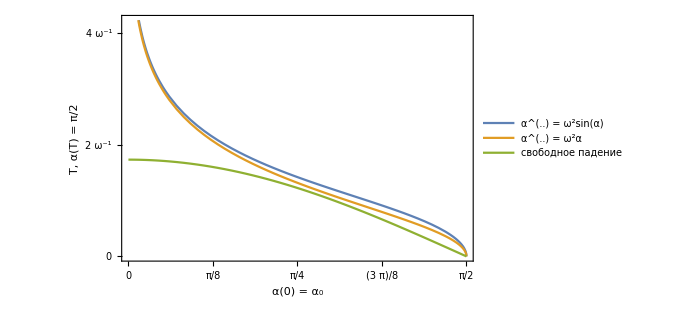

```mathematica
Clear["Global`*"];
a0=0.02;
tmax=6;
l1="α^(..) = ω^2sin(α)";
l2="α^(..) = ω^2α";
l3="свободное падение"
f[a0_]:=t/.FindRoot[Evaluate[a[t]/.NDSolve[{a''[t]==Sin[a[t]],a[0]==a0,a'[0]==0},a,{t,0,5}]]-π/2,{t,1}]⟦1⟧
Show[
Plot[{
f[a0],
ArcCosh[π/(2a0)],
√3 Cos[a0]
},{a0,0.00001,π/2},
PlotRange->Automatic,
ImageSize->500,
Frame->True,
Axes->False,
FrameTicks->{{Table[{i,i"ω^-1"},{i,0,12}],None},{{0,π/8,π/4,3π/8,π/2},None}},
PlotLegends->Placed[LineLegend[{l1,l2,l3}],{Top,Right}],
FrameLabel->{"α(0) = α_0","T, α(T) = π/2"},
LabelStyle->{FontSize->16,FontFamily->"Georgia"}]
(*Plot[π/2,{t,0,tmax},
PlotRange->range,
PlotStyle->Directive[Gray,Dashed]
],
ParametricPlot[{ArcCosh[Pi/(2a0)],y},{y,0,2},
PlotStyle->Directive[Gray,Dotted],
PlotRange->range]*)
]
```

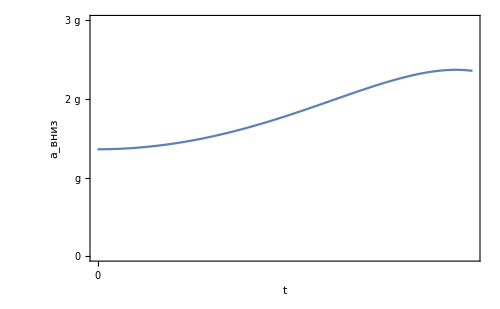

```mathematica
Clear["Global`*"];
a0=Pi/3;
tmax=ArcCosh[π/(2 a0)];
range={{0,tmax},{0,3}};
Show[
Plot[{
3/2 a0 Cosh[t] Sin[a0 Cosh[t]]+3/2 a0^2 Cos[a0 Cosh[t]] Sinh[t]^2
},{t,0,tmax},
PlotRange->range,
ImageSize->500,
Frame->True,
Axes->False,
FrameTicks->{{Table[{i,i"g"},{i,0,3,1}],None},{{{0,0},{1,"ω^-1"},{2,"2ω^-1"},{3,"3ω^-1"},{4,"4ω^-1"},{5,"5ω^-1"},{6,"6ω^-1"}},None}},
FrameLabel->{"t","a_(:0432:043d:0438:0437)"},
LabelStyle->{FontSize->16,FontFamily->"Georgia"}]
(*,
Plot[π/2,{t,0,tmax},
PlotRange->range,
PlotStyle->Directive[Gray,Dashed]
],
ParametricPlot[{ArcCosh[Pi/(2a0)],y},{y,0,2},
PlotStyle->Directive[Gray,Dotted],
PlotRange->range]*)
]
```

```mathematica
Manipulate[
Plot[3/2 α0 Cosh[t] Sin[α0 Cosh[t]]+3/2 α0^2 Cos[α0 Cosh[t]] Sinh[t]^2,{t,0,ArcCosh[π/(2 α0)]},PlotRange->{Automatic,Full}]
,{{α0,0.1},0.0001,1.57}]
```

```mathematica
α[t_]:=α0 Cosh[ω t];
D[α'[t]L Sin[α[t]],t]/.t->ω^-1 τ/.ω->√((3g)/(2L))/.g->1/.τ->t
```

3/2 α0 Cosh[t] Sin[α0 Cosh[t]]+3/2 α0^2 Cos[α0 Cosh[t]] Sinh[t]^2

```mathematica
α'[t]L
```

L α0 ω Sinh[t ω]